{NYSE:MMM,NYSE:AXP,NASDAQ:AAPL,NYSE:BA,NYSE:CAT,NYSE:CVX,NASDAQ:CSCO,NYSE:KO,NYSE:DIS,NYSE:DWDP,NYSE:XOM,NYSE:GE,NYSE:GS,NYSE:HD,NASDAQ:INTC,NYSE:IBM,NYSE:JNJ,NYSE:JPM,NYSE:MCD,NYSE:MRK,NASDAQ:MSFT,NYSE:NKE,NYSE:PFE,NYSE:PG,NYSE:TRV,NYSE:UNH,NYSE:UTX,NYSE:VZ,NYSE:V,NYSE:WMT}

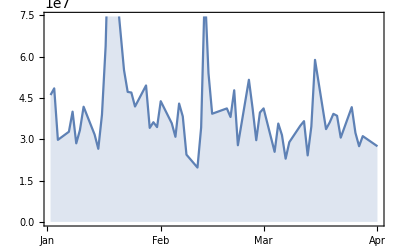

```mathematica
mems=FinancialData["^DJI","Members"]
start={2013,1,1};
end={2013,4,1};
FinancialData["GE",{start,end}];
t=Table[{{{ mems[[i]] },start,end },Transpose[{FinancialData[ToString[mems[[i]]],{start,end}][[All,2]]}]},{i,1,Length[mems]}];

DateListPlot[FinancialData["GE","Volume",{start,end}],Filling->Axis]
```

```mathematica
mems
```

{NYSE:MMM,NYSE:AXP,NASDAQ:AAPL,NYSE:BA,NYSE:CAT,NYSE:CVX,NASDAQ:CSCO,NYSE:KO,NYSE:DIS,NYSE:DWDP,NYSE:XOM,NYSE:GE,NYSE:GS,NYSE:HD,NASDAQ:INTC,NYSE:IBM,NYSE:JNJ,NYSE:JPM,NYSE:MCD,NYSE:MRK,NASDAQ:MSFT,NYSE:NKE,NYSE:PFE,NYSE:PG,NYSE:TRV,NYSE:UNH,NYSE:UTX,NYSE:VZ,NYSE:V,NYSE:WMT}

```mathematica
t
```

Table[{mems⟦i⟧,start,end},FinancialData[ToString[mems⟦i⟧],{start,end}],{i,1,Length[mems]}]

```mathematica
t[[1]]
```

{{NYSE:MMM,{2013,1,1},{2013,4,1}},{{3566073600,94.78},{3566160000,94.67},{3566246400,95.37},{3566505600,95.49},{3566592000,95.5},{3566678400,96.41},{3566764800,96.89},{3566851200,96.28},{3567110400,97.08},{3567196800,97.29},{3567283200,97.6},{3567369600,98.08},{3567456000,98.74},{3567801600,99.33},{3567888000,99.49},{3567974400,99.67},{3568060800,100.59},{3568320000,100.65},{3568406400,101.81},{3568492800,100.8},{3568579200,100.55},{3568665600,101.56},{3568924800,100.77},{3569011200,101.49},{3569097600,102.69},{3569184000,102.22},{3569270400,102.66},{3569529600,102.62},{3569616000,103.46},{3569702400,102.86},{3569788800,102.78},{3569875200,103.23},{3570220800,104.18},{3570307200,103.15},{3570393600,102.72},{3570480000,103.54},{3570739200,101.75},{3570825600,102.31},{3570912000,103.57},{3570998400,104.},{3571084800,103.77},{3571344000,103.28},{3571430400,104.45},{3571516800,104.66},{3571603200,104.54},{3571689600,105.71},{3571948800,105.81},{3572035200,105.13},{3572121600,105.09},{3572208000,106.02},{3572294400,106.4},{3572553600,105.41},{3572640000,105.18},{3572726400,105.66},{3572812800,104.94},{3572899200,106.42},{3573158400,105.17},{3573244800,106.07},{3573331200,105.29},{3573417600,106.31},{3573763200,105.65}}}

```mathematica
Export["C:\Users\matt\Desktop\StockDat\djia4.seqs",t,"List"]
```

C:\Users\matt\Desktop\StockDat\djia4.seqs

```mathematica
t[[1]]
```

{{{NYSE:MMM},{2013,1,1},{2013,4,1}},{{94.78},{94.67},{95.37},{95.49},{95.5},{96.41},{96.89},{96.28},{97.08},{97.29},{97.6},{98.08},{98.74},{99.33},{99.49},{99.67},{100.59},{100.65},{101.81},{100.8},{100.55},{101.56},{100.77},{101.49},{102.69},{102.22},{102.66},{102.62},{103.46},{102.86},{102.78},{103.23},{104.18},{103.15},{102.72},{103.54},{101.75},{102.31},{103.57},{104.},{103.77},{103.28},{104.45},{104.66},{104.54},{105.71},{105.81},{105.13},{105.09},{106.02},{106.4},{105.41},{105.18},{105.66},{104.94},{106.42},{105.17},{106.07},{105.29},{106.31},{105.65}}}